```mathematica
Manipulate[
Module[{di,Ac,P,ΔH,Ua,Ta,Cp,A,Ea,k,R,Q,r,Fao,To,s,p1,p2,p3,rxn},
di=0.25;(*m*)
Ac=(π/4)*di^2;
P=5;(*bar*)
ΔH=If[bn==1,-1,1]*75000;
Ua=500;
Ta=400;
Cp=75;
A=0.1;
Ea=1.16*10^4;
k[temp_]=A*Exp[-Ea/(8.314*(temp+273))];
R=8.314*10^-5;
Q[temp_]=(R*(temp+273))/P*(Fa[z]+Fb[z]);
(*r=-k*Fa[z]*Ac/Q;*)

Fao=0.5;
To=400;

s=If[ta==1,NDSolve[{
Fa'[z]==-k[T[z]]*Fa[z]*Ac/Q[T[z]],
Fb'[z]==-n*k[T[z]]*Fa[z]*Ac/Q[T[z]],
T'[z]==Ac*((-k[T[z]]*Fa[z]*Ac/Q[T[z]])*ΔH-Ua*(T[z]-Ta))/((Fa[z]+Fb[z])*Cp),
Fa[0]==Fao,Fb[0]==0,T[0]==To},{Fa,Fb,T},{z,0,L}],
NDSolve[{
Fa'[z]==-k[Ti]*Fa[z]*Ac/Q[Ti],
Fb'[z]==-n*k[Ti]*Fa[z]*Ac/Q[Ti],
Fa[0]==Fao,Fb[0]==0},{Fa,Fb},{z,0,L}]
];

p1=Plot[{Fa[z]/.s,Fb[z]/.s},{z,0,L},
PlotRange->{0,1.2},
PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.,0.6,0.06]}},
FrameLabel->{Style["distance down reactor (m)",16],Style["molar flow rate (mol/s)",16]}];

If[ta==1,
p2=Plot[T[z]/.s,{z,0,L},
PlotRange->If[bn==1,{400,407},{393,400}],
PlotStyle->{Thick,Black},
FrameLabel->{Style["distance down reactor (m)",16],Style["temperature (K)",16]}]
];

(*p3=Plot[10^4*If[ta==1,Q[T[z]],Q[Ti]]/.s,{z,0,L}];*)

rxn=Graphics[{Text@Style[
If[n==1,"A ⟶ B",Which[
n==0.5,Row[{"A ⟶ ",1/2," B"}],
n==1.5,Row[{"A ⟶ ",3/2," B"}],
n==2,"A ⟶ 2 B",
n==2.5,Row[{"A ⟶ ",5/2," B"}],
n==3,"A ⟶ 3 B"
]],17]},ImageSize->{100,40}];

Show[Switch[cs,1,p1,2,p2],Frame->True,LabelStyle->{Black,13},ImageSize->400,PlotLabel->rxn,ImagePadding->{{55,5},{50,10}}]
],
Grid[{
{Control[{{cs,1,""},{1->"molar flow rate",2->"temperature",3->"volumetric flow"},PopupMenu}]},
{Control[{{bn,1,""},{1->"exothermic",2->"endothermic"},Setter}],
Control[{{ta,1,""},{1->"adiabatic",2->"isothermal"},Setter}]}
},Alignment->Left],

Control[{{n,1,"product reaction coefficient"},0.5,3,0.5,Appearance->"Labeled"}],
Control[{{L,15,"reactor length (m)"},1,25,0.1,Appearance->"Labeled"}]
]
```

NDSolve::ndsz: At z == 2.74991, step size is effectively zero; singularity or stiff system suspected.

```mathematica
(*Grid[{
{Graphics[{Text@Style[
If[n==1,"A ⟶ B",Which[
n==0.5,Row[{"A ⟶ ",1/2," B"}],
n==1.5,Row[{"A ⟶ ",3/2," B"}],
n==2,"A ⟶ 2 B",
n==2.5,Row[{"A ⟶ ",5/2," B"}],
n==3,"A ⟶ 3 B"
]],17]},ImageSize->{200,50}]},
{Show[Switch[cs,1,p1,2,p2],Frame->True,LabelStyle->{Black,13},ImageSize->400,ImagePadding->{{55,5},{50,10}}]}
},Alignment->Center]*)
```

```mathematica
ImageDimensions[-Graphics-]
```

{360,360}

```mathematica
(*Grid[{
{Control[{{cs,2,""},{1->"molar flow rate",2->"temperature"},Setter}],
Control[{{bn,1,"reaction:"},{1->"exothermic",2->"endothermic"},Setter}]},
{Control[{{n,1,"product reaction coefficient"},1,3,0.5,Appearance->"Labeled"}]},
{Control[{{L,25,"reactor length (m)"},1,25,0.1,Appearance->"Labeled"}]}
},Alignment->Left]*)
```

```mathematica
(*{{A,0.1,"A"},0.01,00.1,0.01,Appearance->"Labeled"},
{{Ea,1.16*10^4,"Ea"},10,10^5,Appearance->"Labeled"},*)
```

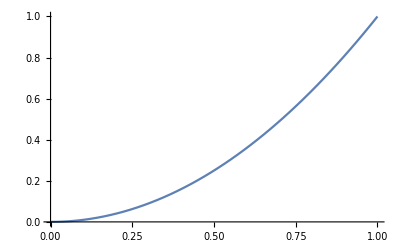

```mathematica
Plot[x^2,{x,0,1},PlotLabel->Graphics[{Text@Style[Row[{1/2," x"}],17]},ImageSize->{50,40}]]
```